intersection (effective TLF temperature) for plot 1 = 0.31 K

intersection (effective TLF temperature) for plot 2 = 0.44 K

intersection (effective TLF temperature) for plot 3 = 0.38 K

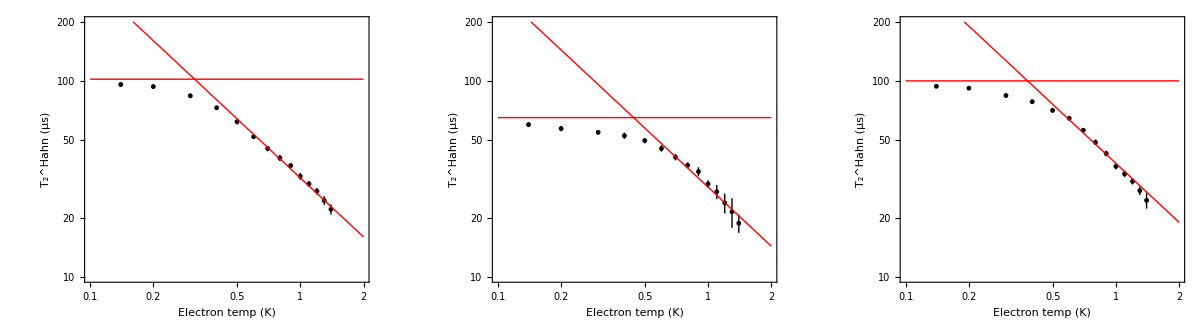

```mathematica
(* Plot of data for T2Hahn versus temperature from Figure 3B of Huang et al., Nature 627,772-777 (2024) *)
(* Data for this paper is deposited at https://doi.org/10.5281/zenodo.10452860 *)
(* Data for T2Hahn versus temperature from Fig. 3B is shown *)

(* 3 data sets: *)
(* triples are temperature, T2Hahn, T2Hahn_error *)

data1={{0.14,0.00009585,0.00000241},{0.2,0.00009354,0.00000240},{0.3,0.00008391,0.00000227},{0.4,0.00007292,0.00000177},{0.5,0.00006188,0.00000191},{0.6,0.00005193,0.00000125},{0.7,0.00004521,0.00000143},{0.8,0.00004047,0.00000147},{0.9,0.00003704,0.00000113},{1,0.00003265,0.00000132},{1.1,0.00002985,0.00000108},{1.2,0.00002741,0.00000106},{1.3,0.00002458,0.00000125},{1.4,0.00002215,0.00000132}};

data2={{0.14,0.00005987,0.00000159},{0.2,0.00005714,0.00000181},{0.3,0.00005470,0.00000142},{0.4,0.00005258,0.00000192},{0.5,0.00004962,0.00000157},{0.6,0.00004526,0.00000172},{0.7,0.00004086,0.00000150},{0.8,0.00003718,0.00000117},{0.9,0.00003449,0.00000182},{1,0.00002986,0.00000128},{1.1,0.00002721,0.00000225},{1.2,0.00002389,0.00000274},{1.3,0.00002153,0.00000369},{1.4,0.00001881,0.00000201}};

data3={{0.14,0.00009384,0.00000178},{0.2,0.00009183,0.00000142},{0.3,0.00008420,0.00000212},{0.4,0.00007828,0.00000201},{0.5,0.00007077,0.00000190},{0.6,0.00006450,0.00000175},{0.7,0.00005605,0.00000148},{0.8,0.00004865,0.00000158},{0.9,0.00004265,0.00000140},{1,0.00003666,0.00000124},{1.1,0.00003359,0.00000128},{1.2,0.00003074,0.00000109},{1.3,0.00002756,0.00000137},{1.4,0.00002462,0.00000226}};

(* change time units to microseconds *)
data1ms=data1;
data1ms[[All,2]]*=10^6;
data1ms[[All,3]]*=10^6;
data2ms=data2;
data2ms[[All,2]]*=10^6;
data2ms[[All,3]]*=10^6;
data3ms=data3;
data3ms[[All,2]]*=10^6;
data3ms[[All,3]]*=10^6;

(* now add lines that are the best fit to a T^-1 dependence for electron temperatures of 0.5 K or higher *)

plot1=ListLogLogPlot[{#1,Around[#2,#3]}&@@@data1ms,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{{"\!\(\*SuperscriptBox[SubscriptBox[\(T\), \(2\)], \(Hahn\)]\) (μs)",None},{"Electron temp (K)",None}},FrameTicks->{{{20,50,100,200,500},None},{{0.1,0.2,0.5,1,2},None}},PlotRange->{{0.1,2},{10,200}},PlotStyle->{Black,PointSize[0.015]},GridLines->{{0.1,0.2,0.3,0.4,0.5,1},{20,50,100,200}},ImageSize->{230,200},AspectRatio->Full];

(*Select data with T>=0.6 and drop uncertainties*)
fitData=Select[data1ms,#[[1]]>=0.6&][[All,{1,2}]];

(*Fit y=A T^-1*)
fit=FindFit[fitData,A x^-1,A,x];
Afit=A/. fit;

(*Fit line that extrapolates but stops at plot edge*)
fitLine=LogLogPlot[Afit x^-1,{x,0.1,2},PlotStyle->{Red,AbsoluteThickness[1]},RegionFunction->Function[{x,y},10<=y<=200]];

(* Add horizontal line at T_2^Hahn of 100 μs, slightly higher than data point at lowest temperature *)
horizontalLine=LogLogPlot[102.,{x,0.1,2},PlotStyle->{Red,AbsoluteThickness[1]}];

(*Combine*)
plot1withlines=Show[plot1,fitLine,horizontalLine];

(* print out location of intersection *)
(*intersection of red lines for plot 1*)
y0=102.;
Teff=Afit/y0;

intersection={Teff,y0};Print["intersection (effective TLF temperature) for plot 1 = ",NumberForm[Teff,{Infinity,2}]," K"]

(* now do plot2 *)

plot2=ListLogLogPlot[{#1,Around[#2,#3]}&@@@data2ms,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{{"\!\(\*SuperscriptBox[SubscriptBox[\(T\), \(2\)], \(Hahn\)]\) (μs)",None},{"Electron temp (K)",None}},FrameTicks->{{{20,50,100,200,500},None},{{0.1,0.2,0.5,1,2},None}},PlotRange->{{0.1,2},{10,200}},PlotStyle->{Black,PointSize[0.015]},GridLines->{{0.1,0.2,0.3,0.4,0.5,1},{20,50,100,200}},ImageSize->{230,200},AspectRatio->Full];

(*Select data with T>=0.6 and drop uncertainties*)
fitData=Select[data2ms,#[[1]]>=0.6&][[All,{1,2}]];

(*Fit y=A T^-1*)
fit=FindFit[fitData,A x^-1,A,x];
Afit=A/. fit;

(*Fit line that extrapolates but stops at plot edge*)
fitLine=LogLogPlot[Afit x^-1,{x,0.1,2},PlotStyle->{Red,AbsoluteThickness[1]},RegionFunction->Function[{x,y},10<=y<=200]];

(* Add horizontal line at T_2^Hahn of 100 μs, slightly higher than data point at lowest temperature *)
horizontalLine=LogLogPlot[65.,{x,0.1,2},PlotStyle->{Red,AbsoluteThickness[1]}];

y0=65.;
Teff=Afit/y0;

intersection={Teff,y0};Print["intersection (effective TLF temperature) for plot 2 = ",NumberForm[Teff,{Infinity,2}]," K"]

(*Combine*)
plot2withlines=Show[plot2,fitLine,horizontalLine];


(* now do plot3 *)

plot3=ListLogLogPlot[{#1,Around[#2,#3]}&@@@data3ms,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{{"\!\(\*SuperscriptBox[SubscriptBox[\(T\), \(2\)], \(Hahn\)]\) (μs)",None},{"Electron temp (K)",None}},FrameTicks->{{{20,50,100,200,500},None},{{0.1,0.2,0.5,1,2},None}},PlotRange->{{0.1,2},{10,200}},PlotStyle->{Black,PointSize[0.015]},GridLines->{{0.1,0.2,0.3,0.4,0.5,1},{20,50,100,200}},ImageSize->{230,200},AspectRatio->Full];

(*Select data with T>=0.6 and drop uncertainties*)
fitData=Select[data3ms,#[[1]]>=0.6&][[All,{1,2}]];

(*Fit y=A T^-1*)
fit=FindFit[fitData,A x^-1,A,x];
Afit=A/. fit;

(*Fit line that extrapolates but stops at plot edge*)
fitLine=LogLogPlot[Afit x^-1,{x,0.1,2},PlotStyle->{Red,AbsoluteThickness[1]},RegionFunction->Function[{x,y},10<=y<=200]];

(* Add horizontal line at T_2^Hahn of 100 μs, slightly higher than data point at lowest temperature *)
horizontalLine=LogLogPlot[100.,{x,0.1,2},PlotStyle->{Red,AbsoluteThickness[1]}];

y0=100.;
Teff=Afit/y0;

intersection={Teff,y0};Print["intersection (effective TLF temperature) for plot 3 = ",NumberForm[Teff,{Infinity,2}]," K"]

(*Combine*)
plot3withlines=Show[plot3,fitLine,horizontalLine];

(* now combine the three plots *)

GraphicsRow[{plot1withlines,plot2withlines,plot3withlines},Spacings->14]
```